# From solutions to problems

Consider a non-moving body hanging vertically from a spring connected to the ceiling. Now, set the body into motion by displacing it from its rest position to a lower position x0. The body oscillates upwards and downwards from its rest position. The motion of the body’s center of mass can be discribed as the position of the center of mass (x) as a function of time, t. This relation may be plotted as

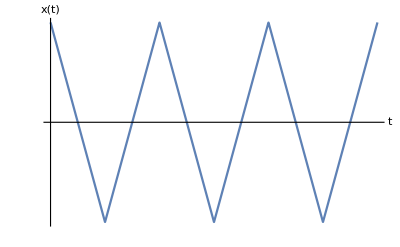

```mathematica
Plot[TriangleWave[t+0.25],{t,0,3},AxesLabel->{t,x[t]},Ticks->None]
```

Notice that the plot shows sharps peaks and valles for certain values of x and so it does not convey the physical idea of “smoothness” that an oscillating body shows. Therefore, we should smooth the plot by means of a smooth function. To establish the function, see that the plot seems to be an approximation of a well-known smooth function: the cosine, whose plot is

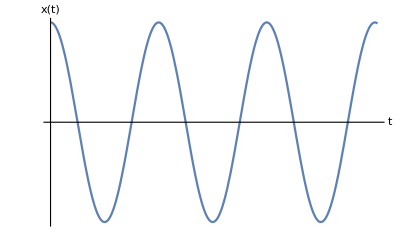

```mathematica
Plot[Cos[t],{t,0,19},AxesLabel->{t,x[t]},Ticks->None]
```

Formally, we can state the relationship as an Ansatz:

```mathematica
x[t_]:=Cos[t]
```

In physics, equations of motion spring from Newton’s second law: f = ma = mx’’

```mathematica
df=D[x[t],{t,2}]+x[t]==0
```

True

```mathematica
tau=2Pi
```

2 π

```mathematica
Resolve[ForAll[ α,α∈Integers,Cos[t]==Cos[t+tau α]]]
```

True